# Test Masking

These tests require the standard test file resources folder to be downloaded from Git and available at Tests/_resources.

## Initialization

```mathematica
<<NounouW`
```

HokahokaW`
Sun 8 Jan 2017 17:56:19     [Mathematica: 11.0.1 for Microsoft Windows (64-bit) (September 20, 2016)]
     Artifact info as of: Sat 7 Jan 2017 13:51:46
     Local repo path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [e39644b3bc228e29af1030f6283774cbaa6717a5]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

<<Set JLink` java stack size to 6144Mb>>

NounouW`
Sun 8 Jan 2017 17:56:19     [Mathematica: 11.0.1 for Microsoft Windows (64-bit) (September 20, 2016)]
     Artifact info as of: Sat 7 Jan 2017 13:50:51
     Local repo path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  master [01ce15654c11e8496083d35b007e0eb7e8fbbce4]
     Remote:  origin (https://github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

```mathematica
Get[ FileNameJoin[{Nest[ParentDirectory,SetDirectory[NotebookDirectory[]],1],"TestDataLoaders.wl"}] ];
$nnwResourcesFolder
```

C:\prog\_w\NounouW\resources

## BG006

```mathematica
NNWTestLoadBG006
```

$nnwTestFileFolder = C:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12

$nnwTestFiles = C:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC13.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC14.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC15.ncsC:\prog\_w\NounouW\resources\nounou\Neuralynx\BG006\2016-06-29_15-33-12\CSC16.ncs

```mathematica
NNPrintInfo[$nnwTestDataOri, "Timing"](*testNCS1@getTiming[]@toStringFull[]*)
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	  19244544 ( 10:01.39) (   601.4)	   261898230 ( 0:00.00)

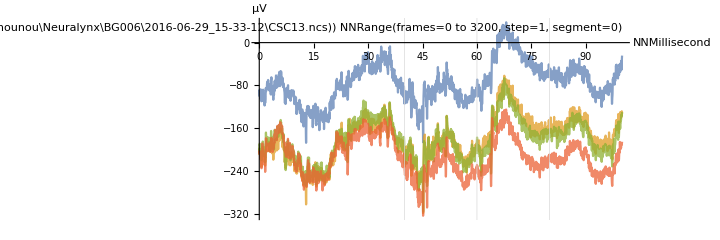

```mathematica
NNTracePlot[$nnwTestDataOri, All, {0 ;; 3200, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}]]
```

### Create mask

```mathematica
tempMask=JavaNew[$NNJavaClass$NNTimestampMask]
```

«JavaObject[nounou.elements.mask.NNTimestampMask]»

```mathematica
tempMask@addMask[ {261920000, 261960000}]
```

```mathematica
tempMask@toString[]
```

NNTimestampMask(count = 1)

```mathematica
tempMask@toStringFull[]
```

nounou.elements.mask.NNTimestampMask(count = 1, 1a58c41332)
==================================================
count		startTs		endTs
     1	   261920000	   261960000

```mathematica
tempMask@addMask[ {261935000, 261940000}]
```

```mathematica
tempMask@toStringFull[]
```

nounou.elements.mask.NNTimestampMask(count = 1, 1a58c41332)
==================================================
count		startTs		endTs
     1	   261920000	   261960000

```mathematica
tempMask@addMask[ {261935000, 261975000}]
```

```mathematica
tempMask@toStringFull[]
```

nounou.elements.mask.NNTimestampMask(count = 1, 1a58c41332)
==================================================
count		startTs		endTs
     1	   261920000	   261975000

```mathematica
tempMask@addMask[ { 261980000,  261990000}]
```

```mathematica
tempMask@toStringFull[]
```

nounou.elements.mask.NNTimestampMask(count = 2, 1a58c41332)
==================================================
count		startTs		endTs
     1	   261920000	   261975000
     2	   261980000	   261990000

### NNTracePlot with mask

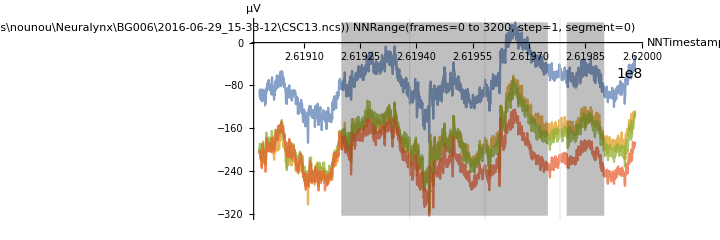

```mathematica
NNTracePlot[$nnwTestDataOri, All, {0 ;; 3200, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit-> NNTimestamp, NNOptMask-> tempMask]
```

```mathematica
tempMasked=NNFilterMasked[$nnwTestDataOri, tempMask]
```

«JavaObject[nounou.elements.data.filters.NNFilterMasked]»

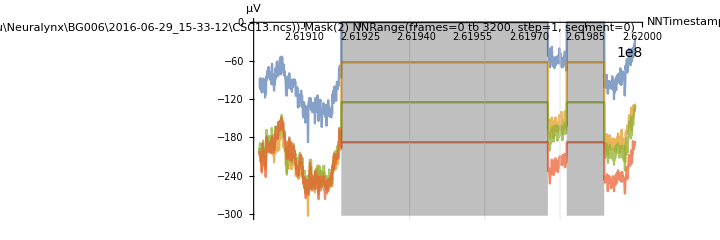

```mathematica
NNTracePlot[tempMasked, All, {0 ;; 3200, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit-> NNTimestamp, NNOptMask-> tempMask]
```

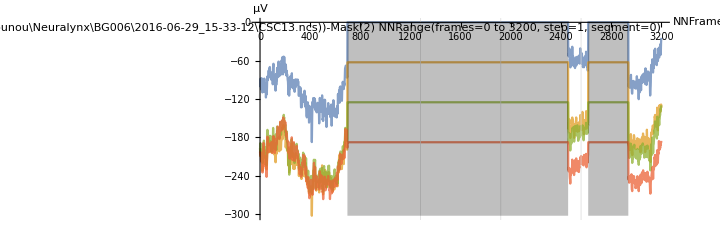

```mathematica
NNTracePlot[tempMasked, All, {0 ;; 3200, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit->NNFrame, NNOptMask-> tempMask]
```

```mathematica
tempMask@addMask[ {863200000,  863220000}];
tempMask@addMask[ {863240000,  863280000}]
```

```mathematica
tempMask@toStringFull[]
```

nounou.elements.mask.NNTimestampMask(count = 4, 1a58c41332)
==================================================
count		startTs		endTs
     1	   261920000	   261975000
     2	   261980000	   261990000
     3	   863200000	   863220000
     4	   863240000	   863280000

```mathematica
tempMasked=NNFilterMasked[$nnwTestDataOri, tempMask]
```

«JavaObject[nounou.elements.data.filters.NNFilterMasked]»

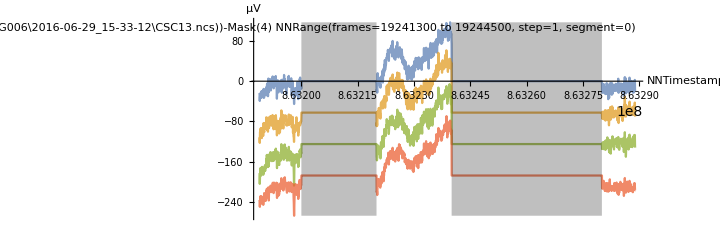

```mathematica
NNTracePlot[tempMasked, All, {19244500-3200 ;; 19244500, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit->NNTimestamp, NNOptMask-> tempMask]
```

```mathematica
tempMask@addMask[ tempMasked,
(NN`NNRange[19239000,19240000, 1, 0])@getValidRange[tempMasked]];
```

```mathematica
tempMask@toStringFull[]
```

nounou.elements.mask.NNTimestampMask(count = 5, 1a58c41332)
==================================================
count		startTs		endTs
     1	   261920000	   261975000
     2	   261980000	   261990000
     3	   863116980	   863148230
     4	   863200000	   863220000
     5	   863240000	   863280000

```mathematica
tempMasked=NNFilterMasked[$nnwTestDataOri, tempMask]
```

«JavaObject[nounou.elements.data.filters.NNFilterMasked]»

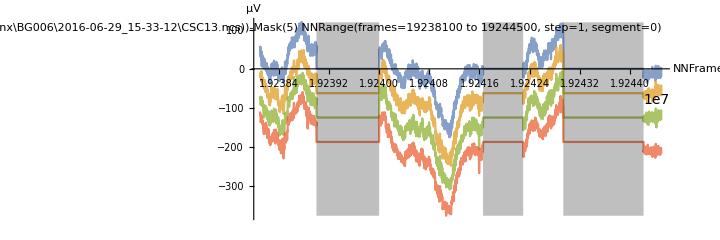

```mathematica
NNTracePlot[tempMasked, All, {19244500-6400 ;; 19244500, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit->NNFrame, NNOptMask-> tempMask]
```

### Rereferencing (not directly relevant)

```mathematica
tempReref=NNFilterTrodeRereference[
NNFilterFIR[$nnwTestDataOri,{10,9000}]
 ]
```

«JavaObject[nounou.elements.data.filters.NNFilterTrodeRereference]»

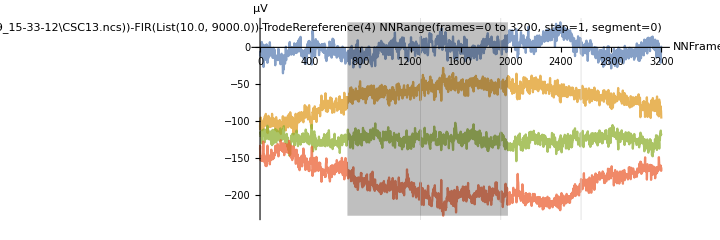

```mathematica
NNTracePlot[tempReref, All, {0 ;; 3200, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit-> NNFrame, NNOptMask-> tempMask]
```

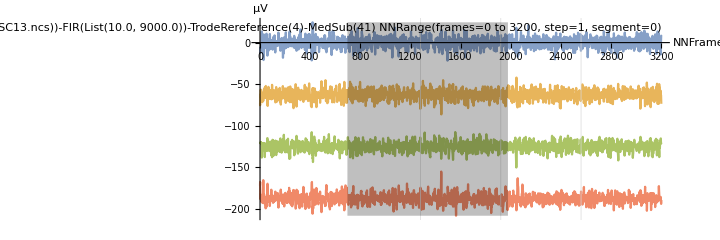

```mathematica
NNTracePlot[NNFilterMedianSubtract[tempReref,41], All, {0 ;; 3200, 0}, 
NNOptAmplificationFactor-> 16, GridLines-> NNMillisecond[{40,60,80}],
NNOptTimeUnit-> NNFrame, NNOptMask-> tempMask]
```